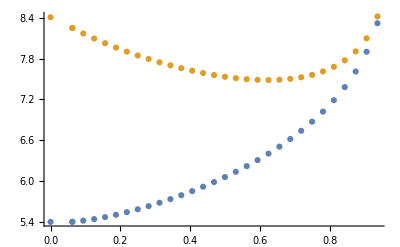

```mathematica
a={{0,5.404137},{0.062500,5.405383},{0.062500,5.405383},{0.093750,5.421956},{0.125000,5.445248},{0.156250,5.474318},{0.187500,5.508337},{0.218750,5.546740},{0.250000,5.589143},{0.281250,5.635300},{0.312500,5.685068},{0.343750,5.738391},{0.375000,5.795289},{0.406250,5.855854},{0.437500,5.920246},{0.468750,5.988696},{0.500000,6.061509},{0.531250,6.139073},{0.562500,6.221867},{0.593750,6.310485},{0.625000,6.405654},{0.656250,6.508282},{0.687500,6.619513},{0.718750,6.740824},{0.750000,6.874191},{0.781250,7.022362},{0.812500,7.189386},{0.843750,7.381690},{0.875000,7.610636},{0.906250,7.900093},{0.937500,8.318570}};
b={{0,8.406441},{0.062500,8.248806},{0.062500,8.248806},{0.093750,8.168343},{0.125000,8.094043},{0.156250,8.025277},{0.187500,7.961336},{0.218750,7.901708},{0.250000,7.846038},{0.281250,7.794094},{0.312500,7.745744},{0.343750,7.700935},{0.375000,7.659693},{0.406250,7.622111},{0.437500,7.588352},{0.468750,7.558647},{0.500000,7.533304},{0.531250,7.512709},{0.562500,7.497344},{0.593750,7.487803},{0.625000,7.484814},{0.656250,7.489286},{0.687500,7.502364},{0.718750,7.525529},{0.750000,7.560758},{0.781250,7.610805},{0.812500,7.679730},{0.843750,7.773978},{0.875000,7.904955},{0.906250,8.096640},{0.937500,8.417920}};
ListPlot[{a,b}]
```

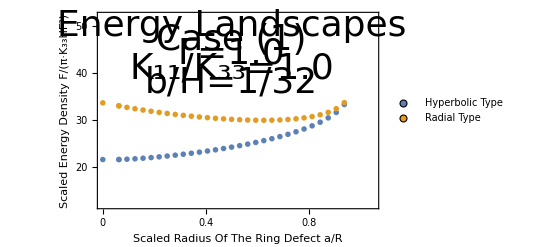

```mathematica
aa=a*Table[{1,4},{i,0,30}];
bb=b*Table[{1,4},{i,0,30}];
ListPlot[{aa,bb},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,30,40,50},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}}, PlotRange->{{0,1.05},{12,52}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Hyperbolic Type","Radial Type"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Energy Landscapes",Directive[Black,36]],{0.5,50}],Text[Style["Case (1)",Directive[Black,36]],{0.5,47}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,44}],
Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.5,41}],
Text[Style["b/H=1/32",Directive[Black,36]],{0.5,38}]}]
```